# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
DeleteDuplicates[Normal[data[All,"WineQuality"]]]
```

{6,5,7,8,4,3,9}

## Utilities

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

```mathematica
standardizer=FeatureExtraction[KeyDrop["WineQuality"]@trainData,"StandardizedVector"];
```

```mathematica
StandardizeData[data_,targetName_,standardizer_]:=Block[
{
featureData=KeyDrop[targetName]@data,
targetData=KeyTake[targetName]@data,
standardizedFeatureData,
featureNames
},
standardizedFeatureData=standardizer[featureData];
featureNames=Flatten[Normal[DeleteDuplicates[Keys[featureData]]]];standardizedFeatureData=Map[<|Map[First[#]->Last[#]&,Partition[Riffle[featureNames,#],2]]|>&,standardizedFeatureData];
Dataset[Merge[#,First]&/@Partition[Riffle[standardizedFeatureData,Normal[targetData]],2]]
]
```

```mathematica
trainData=StandardizeData[trainData,"WineQuality",standardizer];
testData=StandardizeData[testData,"WineQuality",standardizer];
```

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[trainData];
```

```mathematica
GeneraliseValues[values_,scaleFactor_]:=Block[{d,min,max,newValues},
{min,max}=scaleFactor MinMax[values];
Sort[Join[values,{min,max}]]
]
```

```mathematica
(* Generalise the target feature values *)
featureValues["WineQuality"]=GeneraliseValues[featureValues["WineQuality"],1.2]
```

{3,3.6,4,5,6,7,8,9,10.8}

```mathematica
encoders=Map[RealEncoderDecoder[#,0.5]&,featureValues];
```

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],-1]]
]];
```

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],-1]]];
```

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

1136

```mathematica
NetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

## Define neural logic net

```mathematica
ParallelDecisionListWithLearnableActions[conditionSize_,actionSize_,depth_]:=HardNeuralDecisionList[
ConditionActionLayers[Table[
{
NetChain[{HardNeuralOR[neuralLogicInputSize,conditionSize][[1]],ReshapeLayer[{conditionSize}]}],
(*HardNeuralOR[neuralLogicInputSize,conditionSize][[1]]*)
BalancedSoftBits[actionSize][[1]]
}, 
depth
],
BalancedSoftBits[actionSize][[1]]
]
]
```

```mathematica
ParallelDecisionListWithLearnableActions[4,8,1]
```

NetGraph[<>]

```mathematica
CountableActionList[actionSize_,numActions_]:=Module[{actionsPerSize=Max[1,Round[numActions/actionSize]]},
Flatten[Table[RandomChoice[ResourceFunction["SelectTuples"][{0,1},actionSize,Count[#,1]==i&],actionsPerSize],{i,1,actionSize}],1]
]
```

```mathematica
CountableActionList[4,5]
```

{{0,0,0,1},{1,0,1,0},{1,1,1,0},{1,1,1,1}}

```mathematica
CountableActionList[8,32]
```

{{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,1,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,1,0,0,1,0,0},{0,0,1,1,0,0,0,0},{1,0,0,0,1,0,0,1},{0,0,0,0,1,0,1,1},{1,1,0,1,0,0,0,0},{0,0,1,1,0,0,1,0},{1,1,0,0,1,0,1,0},{0,0,1,1,1,1,0,0},{0,1,0,1,1,1,0,0},{0,0,1,0,0,1,1,1},{1,0,1,1,0,0,1,1},{1,0,0,0,1,1,1,1},{1,0,0,1,1,1,0,1},{1,1,1,0,1,1,0,0},{0,1,0,1,1,1,1,1},{1,1,0,0,1,1,1,1},{1,1,1,0,1,1,1,0},{1,1,1,0,1,1,0,1},{1,1,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
CountableActionList[4,16]
```

{{0,0,1,0},{0,1,0,0},{0,0,1,0},{1,0,0,0},{1,0,1,0},{0,1,0,1},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,1,1},{0,1,1,1},{1,1,0,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
SequentialDecisionListWithFixedActions[conditionSize_,actions_List,defaultAction_]:=Module[{actionSize=Length[actions]},
HardNeuralDecisionList[
ConditionActionLayers[Map[{
NetChain[{HardNeuralOR[neuralLogicInputSize,conditionSize][[1]],(* TODO *)HardNeuralOR[neuralLogicInputSize,1][[1]],ReshapeLayer[{1}]}],
NetArrayLayer["Array"->#,"Output"->Length[#],LearningRateMultipliers->None]
}&,
actions],
NetArrayLayer["Array"->defaultAction,"Output"->Length[defaultAction],LearningRateMultipliers->None]
]
]
]
```

```mathematica
SequentialDecisionListWithFixedActions[4,CountableActionList[16,32],Table[0,16]]
```

NetGraph[<>]

```mathematica
NeuralLogicPredictor[decisionList_]:={NetGraph[<|
"DecisionList"->decisionList,
"Flatten"->FlattenLayer[],
"Real"->HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]][[1]],
"Reshape"->ReshapeLayer[{}]
|>,
{
"DecisionList"->"Flatten",
"Flatten"->"Real",
"Real"->"Reshape"
}
],#&}
```

```mathematica
tmp=NeuralLogicPredictor[SequentialDecisionListWithFixedActions[4,CountableActionList[16,32],Table[0,16]]][[1]]
```

NetGraph[<>]

```mathematica
tmp[Table[1,neuralLogicInputSize]]
```

3.4875

```mathematica
NeuralLogicNet[predictor_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=predictor;
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet
|>,
{"FeatureLayer"->"SoftNet",NetPort["SoftNet","Output"]->NetPort["WineQuality"]}
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
Method->{"ADAM"},
TargetDevice->"GPU",
PerformanceGoal->"TrainingSpeed",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=Association/@ResourceFunction["DynamicMap"][{
"Prediction"->First[hardNetFunction[Harden[Normal[featureLayer[#]]]]],
"Target"->#[targetName]
}&,
Normal[data]
]
]
```

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A neural logic network

```mathematica
(* Type 1 *)
actionList=RandomSample[CountableActionList[(* action size *)16,(* num actions *)16]];
decisionList=SequentialDecisionListWithFixedActions[(* condition size *)1,Echo[actionList],Table[0,16]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,1,1,1,0,0,1,0,1,1},{1,1,0,0,1,1,0,1,1,1,0,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,0,0,1,0,0,1,0,1,1},{1,1,1,1,1,1,1,0,0,1,0,1,1,1,1,1},{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,1,0,0,1,1,1,1,0,0,1,1,1,0,0,0},{0,1,1,0,0,1,1,1,0,0,1,1,1,1,0,1},{1,1,0,1,1,0,1,0,0,0,0,0,0,1,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0},{1,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0},{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,0,0,0,1,1,0,0,0,0,1,0,1,1,0}}

NetGraph[<>]

```mathematica
(* Type 2 *)
decisionList=ParallelDecisionListWithLearnableActions[(* condition size *)32,(* action size *)32,(* depth *)4]
```

NetGraph[<>]

```mathematica
(* Narrow and deep performs poorly *)
decisionList=ParallelDecisionListWithLearnableActions[(* condition size *)1,(* action size *)32,(* depth *)8]
```

NetGraph[<>]

```mathematica
(* Trainable net *)
{softNet,hardNet}=NeuralLogicNet[NeuralLogicPredictor[decisionList]];
```

```mathematica
NetFlatten[softNet,Infinity]
```

NetGraph[<>]

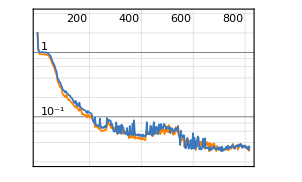
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3274  rounds:818  time:2.5min  examples/s:1399
data | ,,  training examples:200  validation examples:200  processed examples:209536  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.28×10^-2
validation | ,,  loss:3.59×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=Block[{td=Take[trainData,200],vd=testData},
vd=td;
TrainNeuralLogicNet[softNet,td,vd]
]
```

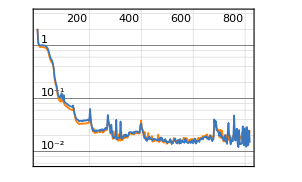
```mathematica
(* Version 1 *)
NetTrainResultsObject[{{"NetTrain Results"}, {{{summary, ,"," " "batches:3272 " "rounds:818 " "time:2.8min " "examples/s:1248}, {data, ,"," " "training examples:200 " "validation examples:200 " "processed examples:209408 " "skipped examples:0}, {method, ,"," " "ADAMoptimizer " "batch size64GPU}, {round, ,"," " "loss:"3.82"×10^("-2")}, {validation, ,"," " "loss:"1.24"×10^("-2")}, {{{, "rounds"}, {"loss", -Graphics-}}, }, {-Graphics-  "training set"	-Graphics-  "validation set", }}}}]
```

```mathematica
(* Version 2 *)
NetTrainResultsObject[{{"NetTrain Results"}, {{{summary, ,"," " "batches:3274 " "rounds:818 " "time:2.5min " "examples/s:1399}, {data, ,"," " "training examples:200 " "validation examples:200 " "processed examples:209536 " "skipped examples:0}, {method, ,"," " "ADAMoptimizer " "batch size64GPU}, {round, ,"," " "loss:"3.28"×10^("-2")}, {validation, ,"," " "loss:"3.59"×10^("-2")}, {{{, "rounds"}, {"loss", -Graphics-}}, }, {-Graphics-  "training set"	-Graphics-  "validation set", }}}}]
```

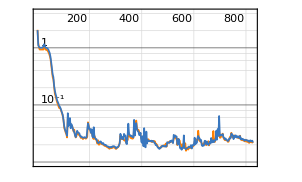
```mathematica
(* Version 3 *)
NetTrainResultsObject[{{"NetTrain Results"}, {{{summary, ,"," " "batches:3308 " "rounds:827 " "time:3.0min " "examples/s:1176}, {data, ,"," " "training examples:200 " "validation examples:200 " "processed examples:211712 " "skipped examples:0}, {method, ,"," " "ADAMoptimizer " "batch size64GPU}, {round, ,"," " "loss:"2.16"×10^("-2")}, {validation, ,"," " "loss:"2.06"×10^("-2")}, {{{, "rounds"}, {"loss", -Graphics-}}, }, {-Graphics-  "training set"	-Graphics-  "validation set", }}}}]
```

```mathematica
(* 
Min/Max approach: round: ~0.05
My piecewise approach: fails to converge, unstable.
*)
```

```mathematica
trainedNeuralLogicNet=result["TrainedNet"];
```

```mathematica
NetMeasurements[trainedNeuralLogicNet,testData,{"RSquared"}]
```

{0.388737}

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
(* Jump ahead to predictions to save time *)
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize]
```

```mathematica
predictions=NeuralLogicPredict[testData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer];
```

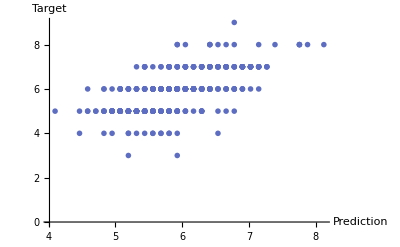

```mathematica
ListPlot[{{Missing[]},predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->{"DarkColor","OpenMarkers"}]
```

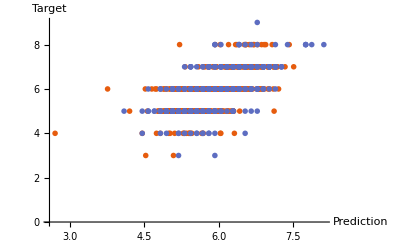

```mathematica
ListPlot[{standardPredictions,predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->{"DarkColor","OpenMarkers"}]
```

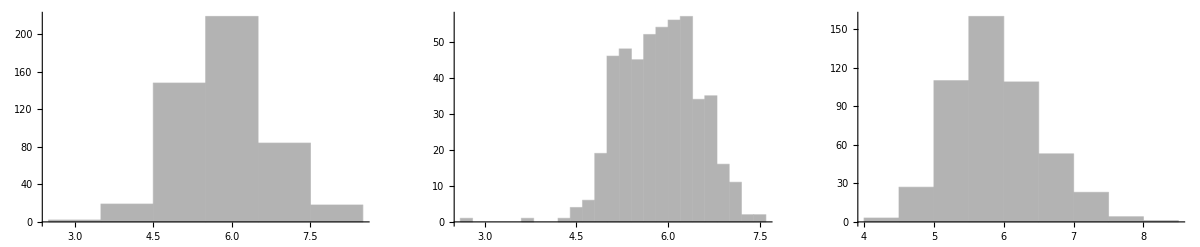

```mathematica
GraphicsRow[Histogram[#,PlotRange->All,PlotTheme->"Monochrome"]&/@{#["Target"]&/@standardPredictions,#["Prediction"]&/@standardPredictions,#["Prediction"]&/@predictions}]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

8.875 kB

```mathematica
#["NumBits"]&/@KeyDrop[encoders,"WineQuality"]
```

<|FixedAcidity→35,VolatileAcidity→62,CitricAcid→42,ResidualSugar→155,Chlorides→79,FreeSulfurDioxide→65,TotalSulfurDioxide→126,Density→430,PH→51,Sulphates→39,Alcohol→51|>

```mathematica
encoderSize=Quantity[Total[Values[#["NumBits"]&/@KeyDrop[encoders,"WineQuality"]]]*32.0/1024,"Kilobytes"]
```

35.4688 kB

```mathematica
totalNeuralLogicNetSize=neuralLogicNetSize+encoderSize
```

44.3438 kB

```mathematica
standardNetSize
```

536. kB

## Notes

```mathematica
neuralLogicPredictions=NetPredict[trainedNeuralLogicNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@neuralLogicPredictions],MinMax[#["Target"]&/@neuralLogicPredictions]}
```

{{4.52344,8.05781},{3,9}}

```mathematica
ListPlot[Values/@neuralLogicPredictions]
```